# NG^21 P_03.Метод главных компонент

Бельская Екатерина, 5 группа, 2 курс

## 1. Гистограмма

```mathematica
Dimensions[dataSet = First@Import["C:\\NG\\NG21P03Problem.xlsx"]]
```

{2504,25}

```mathematica
dataSet
```

Список меток, обозначающих пол человека

```mathematica
Dimensions[trainLable=dataSet⟦5;;,1⟧]
```

{2500}

Образцы train

```mathematica
Dimensions[train=dataSet⟦5;;,2 ;;⟧]
```

{2500,24}

Гистограмма для параметра роста

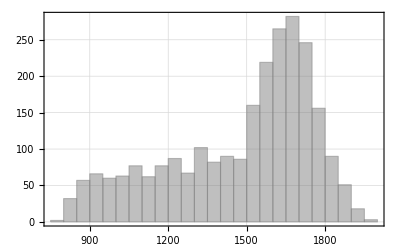

```mathematica
Histogram[{train⟦All,2⟧}, Frame->True, GridLines->Automatic, ChartStyle->GrayLevel[0.5,0.5]]
```

Позиции в списке, на которых "располагаются" мужчины

```mathematica
Dimensions[indexMale=Position[trainLable,"М"]//Flatten]
```

{1250}

Позиции в списке, на которых "располагаются" женщины

```mathematica
Dimensions[indexFemale=Position[trainLable,"Ж"]//Flatten]
```

{1250}

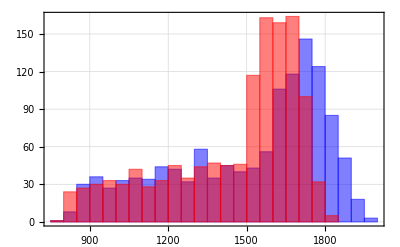

```mathematica
Histogram[{train⟦indexMale,2⟧,train⟦indexFemale,2⟧}, Frame->True, GridLines->Automatic, ChartStyle->{Blue, Red}]
```

Функция, находящая позиции в train, на которых находятся люди старше a и младше b

```mathematica
indexAge[a_,b_]:=Position[train⟦All,1⟧,#]&/@(N@Range[a,b])//Flatten
```

```mathematica
Manipulate[Histogram[If[v==1,train⟦Intersection[Range[Length@train],#],u⟧,
{train⟦Intersection[indexMale,#],u⟧,train⟦Intersection[indexFemale,#],u⟧}]&@indexAge[a⟦1⟧,a⟦2⟧],30,Frame->True, GridLines->Automatic,If[v==1,ChartStyle->GrayLevel[0.5,0.5],ChartStyle->{Blue, Red}]],
{{v,1,"Пол" },{1->"Все",2->"M/Ж"}} ,{{a,{20,60},"Возраст"},1,80},{{u,2,"Параметры"},Range[2,24]}, ControlType->{SetterBar,IntervalSlider,SetterBar}]
```

Ps : В Manipulate не знаю, как сделать как сделать рост динамическим параметром

## 2. Стандартизация данных

Среднее значение и стандартное отклонение для каждого параметра

```mathematica
kmμ=Mean[train]
kmσ=StandardDeviation[train]
```

{23.8064,1476.85,1360.2,1192.92,916.577,645.105,1741.03,774.937,667.744,498.614,205.482,378.277,126.85,412.563,504.044,355.027,635.752,213.55,307.369,368.098,161.782,73.5216,222.628,85.908}

{23.0579,278.211,274.841,239.833,187.987,134.605,341.466,130.606,127.055,97.0148,41.7676,80.5595,27.5609,99.6577,113.825,67.9879,132.017,51.6316,78.499,74.2269,30.2852,12.8598,40.2248,13.6605}

Стандартизованные данные

```mathematica
Dimensions[Data=MapThread[(#1-#2)/#3&,{trainᵀ, kmμ,kmσ}]ᵀ]
```

{2500,24}

```mathematica
Mean[Data]//Chop
StandardDeviation[X]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## 3. "Правило трех сигм"

Функция, вычисляющая процент значений, попадающих в каждый из восьми интервалов. Результат : данные в строковом виде

```mathematica
intvalue[u_]:=Map[StringForm["``%",NumberForm[#,{∞,2}]]&,1/Length[Data] BinCounts[Data⟦All,u⟧,{{-∞,-3,-2,-1,0,1,2,3,∞}}]100.]
```

```mathematica
line=Map[StringForm["``σ",#]&,Cases[Range[-3,3],Except[0]]]//Insert[#,"...",{{1},{-1}}]&;
```

```mathematica
line1={"0.1%","2.1%","13.6%","34.1%"}//Join[#,Reverse@#]&
```

{0.1%,2.1%,13.6%,34.1%,34.1%,13.6%,2.1%,0.1%}

```mathematica
Manipulate[Grid[{line,line1,intvalue[u]},Frame->All,Background->{None,{Gray}}],{{u,2,"Параметры"},Range[2,24]},ControlType->SetterBar]
```

## 4. Сингулярное разложение матрицы

```mathematica
Map[Dimensions,{U, S, V}=SingularValueDecomposition[Data]]
```

{{2500,2500},{2500,24},{24,24}}

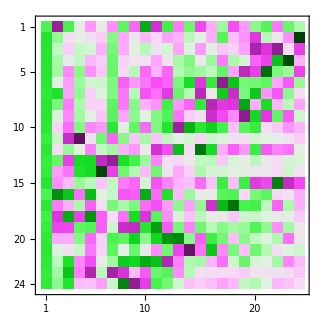

```mathematica
MatrixPlot[V,ColorFunction->"GreenPinkTones"]
```

```mathematica
MatrixPlot[U,ColorFunction->"GreenPinkTones"]
```

-Graphics-

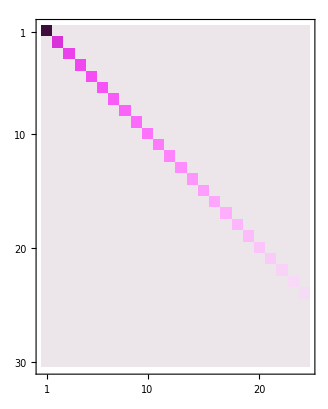

```mathematica
MatrixPlot[Take[S,30],ColorFunction->"GreenPinkTones"]
```

{222.053,60.5553,31.9066,26.4274,25.5294,23.4354,21.9025,20.1785,19.2563,17.3589,16.6198,15.712,14.7321,14.2131,13.9098,13.5581,13.4473,13.3625,12.6298,12.2245,12.1044,11.7314,11.3515,11.1582}

{222.053,60.5553,31.9066,26.4274,25.5294,23.4354,21.9025,20.1785,19.2563,17.3589,16.6198,15.712,14.7321,14.2131,13.9098,13.5581,13.4473,13.3625,12.6298,12.2245,12.1044,11.7314,11.3515,11.1582}

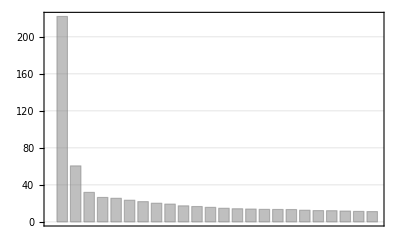

```mathematica
SV=Diagonal[S]
SingularValueList[Data]
BarChart[%,Frame->True,GridLines->Automatic,ChartStyle->GrayLevel[0.5,0.5]]
```

Абсолютная и относительная погрешности

```mathematica
Δ=Chop@Norm[Data-U⟦All,Range[#]⟧.S⟦Range[#],Range[#]⟧.V⟦All,Range[#]⟧ᵀ]&/@Range[24]
```

{60.5553,31.9066,26.4274,25.5294,23.4354,21.9025,20.1785,19.2563,17.3589,16.6198,15.712,14.7321,14.2131,13.9098,13.5581,13.4473,13.3625,12.6298,12.2245,12.1044,11.7314,11.3515,11.1582,0}

```mathematica
σ=Δ/Norm[Data]
```

{0.272707,0.14369,0.119014,0.11497,0.10554,0.0986367,0.0908726,0.0867194,0.0781748,0.0748464,0.0707582,0.0663451,0.0640077,0.0626421,0.0610582,0.0605592,0.0601771,0.0568775,0.0550523,0.0545114,0.0528319,0.051121,0.0502504,0.}

```mathematica
σstr=Map[StringForm["``%",NumberForm[#,{∞,2}]]&,σ *100.]
```

{27.27%,14.37%,11.90%,11.50%,10.55%,9.86%,9.09%,8.67%,7.82%,7.48%,7.08%,6.63%,6.40%,6.26%,6.11%,6.06%,6.02%,5.69%,5.51%,5.45%,5.28%,5.11%,5.03%,0.00%}

```mathematica
Grid[{Range[24],SV,ConstantArray[Norm[Data],24],Δ,σstr}ᵀ//Prepend[#,{"n","SV","Data","Δ","σ"}]&,Frame->All,Background->{{LightGray,None},{Gray,{White, LightBlue}}}]
```

n | SV | Data | Δ | σ
1 | 222.053 | 222.053 | 60.5553 | 27.27%
2 | 60.5553 | 222.053 | 31.9066 | 14.37%
3 | 31.9066 | 222.053 | 26.4274 | 11.90%
4 | 26.4274 | 222.053 | 25.5294 | 11.50%
5 | 25.5294 | 222.053 | 23.4354 | 10.55%
6 | 23.4354 | 222.053 | 21.9025 | 9.86%
7 | 21.9025 | 222.053 | 20.1785 | 9.09%
8 | 20.1785 | 222.053 | 19.2563 | 8.67%
9 | 19.2563 | 222.053 | 17.3589 | 7.82%
10 | 17.3589 | 222.053 | 16.6198 | 7.48%
11 | 16.6198 | 222.053 | 15.712 | 7.08%
12 | 15.712 | 222.053 | 14.7321 | 6.63%
13 | 14.7321 | 222.053 | 14.2131 | 6.40%
14 | 14.2131 | 222.053 | 13.9098 | 6.26%
15 | 13.9098 | 222.053 | 13.5581 | 6.11%
16 | 13.5581 | 222.053 | 13.4473 | 6.06%
17 | 13.4473 | 222.053 | 13.3625 | 6.02%
18 | 13.3625 | 222.053 | 12.6298 | 5.69%
19 | 12.6298 | 222.053 | 12.2245 | 5.51%
20 | 12.2245 | 222.053 | 12.1044 | 5.45%
21 | 12.1044 | 222.053 | 11.7314 | 5.28%
22 | 11.7314 | 222.053 | 11.3515 | 5.11%
23 | 11.3515 | 222.053 | 11.1582 | 5.03%
24 | 11.1582 | 222.053 | 0 | 0.00%

## 5. Выделение главных компонент

```mathematica
ClearAll[toPC];
toPC[param_List, n_Integer]:=(param.V)⟦n⟧;
toPC[param_List]:=param.V;
```

```mathematica
PC=toPC[Data⟦#⟧]&/@Range[Length@Data];
```

## 6. Ковариационная матрица

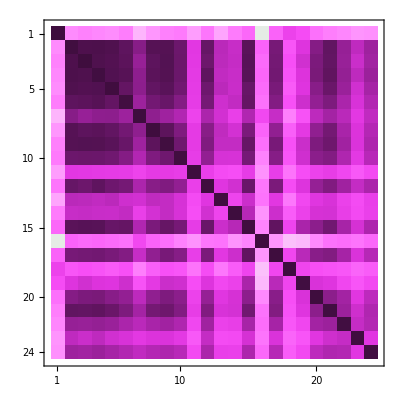

```mathematica
MatrixPlot[Covariance[Data],ColorFunction->"GreenPinkTones"]
```

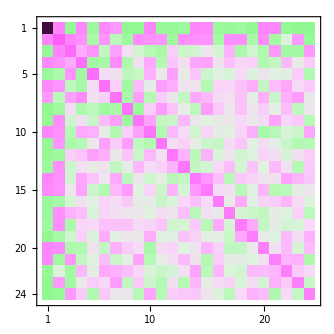

```mathematica
MatrixPlot[Covariance[PC],ColorFunction->"GreenPinkTones"]
```

## 7. Эллипс рассеивания

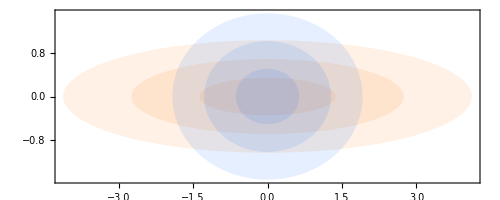

```mathematica
Chop@{Mean[PC⟦All,3⟧],Mean[PC⟦All,5⟧]};
Covariance[PC⟦All,{3,5}⟧];
Chop@{Mean[Data⟦All,3⟧],Mean[Data⟦All,5⟧]};
Covariance[Data⟦All,{3,5}⟧];
Graphics[{Hue[.08, 1, 1, 0.1],Ellipsoid[%%,%],Ellipsoid[%%,4%],Ellipsoid[%%,9%],Hue[.6, 1, 1, 0.1],Ellipsoid[%%%%,%%%],Ellipsoid[%%%%,4%%%],Ellipsoid[%%%%,9%%%]},PlotRange->All,Frame->True]
```

```mathematica
r=Power[Range[3],2]
```

{1,4,9}

```mathematica
Manipulate[Graphics[{Hue[.08, 1, 1, 0.1],Ellipsoid[Chop@Map[Mean, {Data⟦All,u⟧,Data⟦All,v⟧}],#*Covariance[Data⟦All,{u,v}⟧]]&/@r,Hue[.6, 1, 1, 0.1],Ellipsoid[Chop@Map[Mean, {PC⟦All,u⟧,PC⟦All,v⟧}],#*Covariance[PC⟦All,{u,v}⟧]]&/@r},PlotRange->All,Frame->True],{{u,2,"Вер"},Range[24]},{{v,1,"Гор"},Range[24]},ControlType->SetterBar]
```

## 8. Эллипсоид рассеивания

```mathematica
Manipulate[Graphics3D[{Hue[.08, 1, 1, 0.1],Ellipsoid[Chop@Map[Mean, {Data⟦All,u⟧,Data⟦All,v⟧,Data⟦All,w⟧}],#*Covariance[Data⟦All,{u,v,w}⟧]]&/@r,Hue[.6, 1, 1, 0.1],Ellipsoid[Chop@Map[Mean, {PC⟦All,u⟧,PC⟦All,v⟧,PC⟦All,w⟧}],#*Covariance[PC⟦All,{u,v,w}⟧]]&/@r},PlotRange->All],{{u,2,"1ый"},Range[24]},{{v,1,"2ой"},Range[24]},{{w,1,"3ий"},Range[24]},ControlType->SetterBar]
```